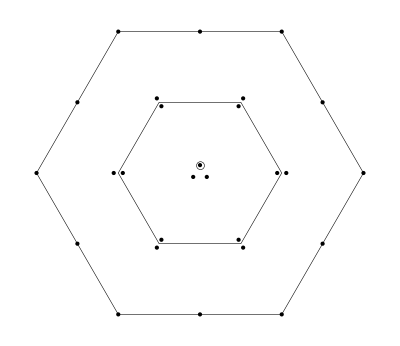

Y=0,  I_3=0

-6uuūū-2ddd̄d̄-2sss̄s̄+3(ud+du)(ūd̄+d̄ū)+3(us+su)(ūs̄+s̄ū)-(sd+ds)(s̄d̄+d̄s̄)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C γ^μ s_b) ((d̄)_a γ^μ C((s̄)_b)^T-(d̄)_b γ^μ C((s̄)_a)^T)+(s_a^T C γ^μ d_b) ((d̄)_a γ^μ C((s̄)_b)^T-(d̄)_b γ^μ C((s̄)_a)^T)+(d_a^T C γ^μ s_b) ((s̄)_a γ^μ C((d̄)_b)^T-(s̄)_b γ^μ C((d̄)_a)^T)+(s_a^T C γ^μ d_b) ((s̄)_a γ^μ C((d̄)_b)^T-(s̄)_b γ^μ C((d̄)_a)^T)+2 (d_a^T C γ^μ d_b) ((d̄)_a γ^μ C((d̄)_b)^T-(d̄)_b γ^μ C((d̄)_a)^T)+3 (d_a^T C γ^μ u_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+3 (u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+3 (d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+3 (u_a^T C γ^μ d_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+2 (s_a^T C γ^μ s_b) ((s̄)_a γ^μ C((s̄)_b)^T-(s̄)_b γ^μ C((s̄)_a)^T)+3 (s_a^T C γ^μ u_b) ((s̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((s̄)_b)^T)+3 (u_a^T C γ^μ s_b) ((s̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((s̄)_b)^T)+3 (s_a^T C γ^μ u_b) ((ū)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((ū)_b)^T)+3 (u_a^T C γ^μ s_b) ((ū)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((ū)_b)^T)+6 (u_a^T C γ^μ u_b) ((ū)_a γ^μ C((ū)_b)^T-(ū)_b γ^μ C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-2 (d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 d)+2 (d̄ γ^μ d d̄ γ^μ d)-4 (d̄(γ̄)^5 d d̄(γ̄)^5 d)-2 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s)-2 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d)+2 (d̄ γ^μ d s̄ γ^μ s)+2 (d̄ γ^μ s s̄ γ^μ d)-4 (d̄(γ̄)^5 s s̄(γ̄)^5 d)+4 (d̄(γ̄)^5 d) (3 (ū(γ̄)^5 u)-s̄(γ̄)^5 s)+4 (d̄ 1d) (s̄ 1s-3 (ū 1u))+4 (d̄ 1s s̄ 1d)+6 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+6 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-6 (d̄ γ^μ d ū γ^μ u)-6 (d̄ γ^μ u ū γ^μ d)+12 (d̄(γ̄)^5 u ū(γ̄)^5 d)-12 (d̄ 1u ū 1d)+4 (d̄ 1d d̄ 1d)-2 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)+2 (s̄ γ^μ s s̄ γ^μ s)-4 (s̄(γ̄)^5 s s̄(γ̄)^5 s)+6 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+6 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)-6 (s̄ γ^μ s ū γ^μ u)-6 (s̄ γ^μ u ū γ^μ s)+12 (s̄(γ̄)^5 s ū(γ̄)^5 u)+12 (s̄(γ̄)^5 u ū(γ̄)^5 s)-12 (s̄ 1s ū 1u)-12 (s̄ 1u ū 1s)+4 (s̄ 1s s̄ 1s)-6 (ū(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)+6 (ū γ^μ u ū γ^μ u)-12 (ū(γ̄)^5 u ū(γ̄)^5 u)+12 (ū 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(32 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(8 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (10 m_d-m_s-9 m_u) q^4)/(3 π^4)+(3 ⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-2 m_u) q^4)/π^4+(⟨ s̄ s⟩ log(-q^2/μ^2) (m_d-10 m_s+9 m_u) q^4)/(3 π^4)-(40 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(40 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(168 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(125 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(144 π^6)-(72 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(120 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(120 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(4 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(2 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(6 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(2 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(4 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(6 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(6 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(6 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(12 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(12 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(12 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(44 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(11 ⟨ d̄ Gd⟩^2)/(48 π^2 q^2)-(11 ⟨ s̄ Gs⟩^2)/(48 π^2 q^2)-(33 ⟨ ū Gu⟩^2)/(16 π^2 q^2)-(68 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(3 π q^2)+(52 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)+(52 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)-(11 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(48 π^2 q^2)-(33 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(16 π^2 q^2)-(33 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(16 π^2 q^2)-(64 ⟨ d̄ d⟩^3 m_d)/q^2-(64 ⟨ s̄ s⟩^3 m_s)/q^2-(32 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (25 m_d+2 m_s))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (2 m_d+25 m_s))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_d-23 m_u))/q^2-(32 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (2 m_s-23 m_u))/q^2+(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (m_d+m_s-3 m_u))/q^2+(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (7 m_d-2 m_u))/q^2+(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (7 m_s-2 m_u))/q^2-(576 ⟨ ū u⟩^3 m_u)/q^2

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

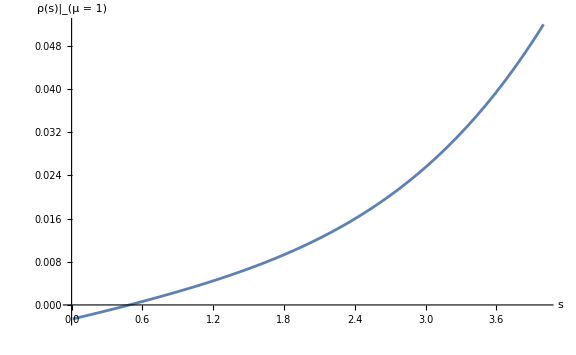
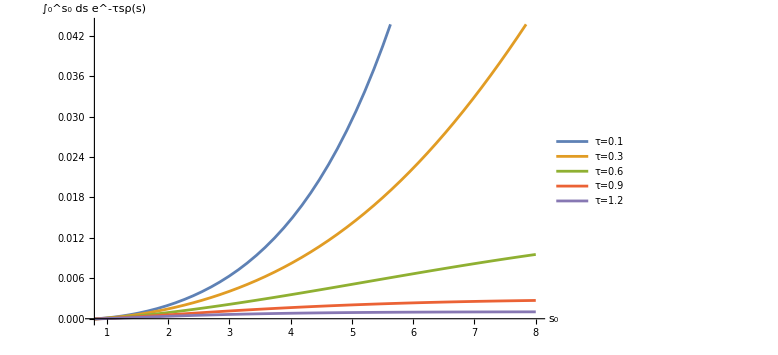

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

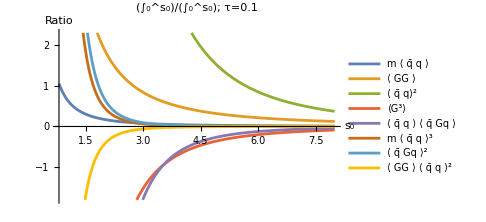
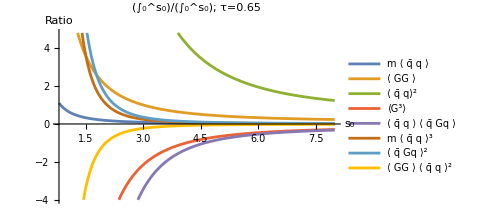
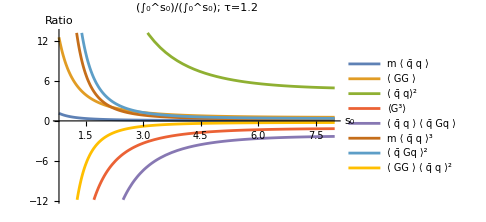

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

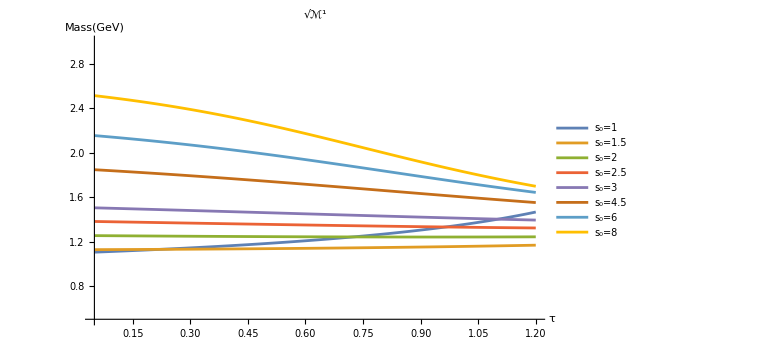
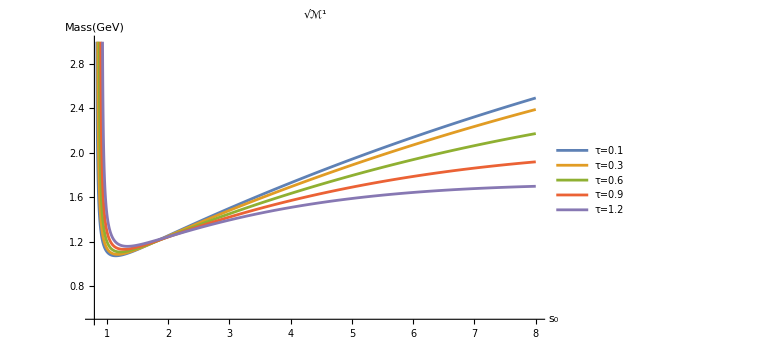

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

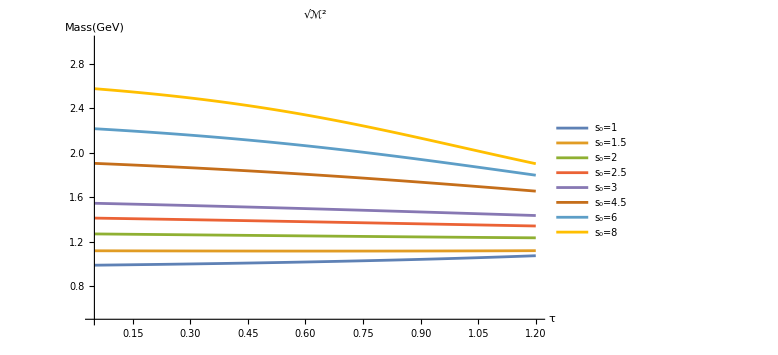
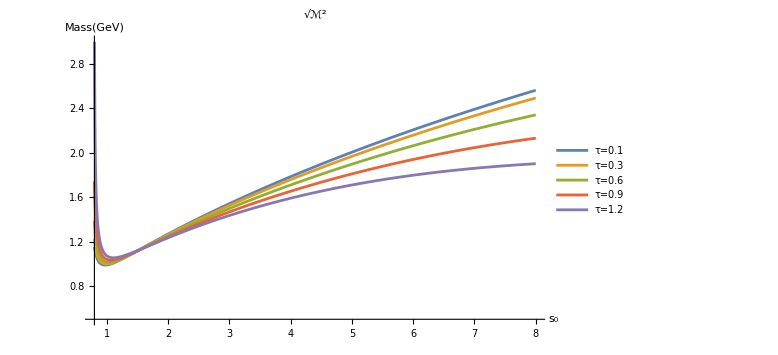

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

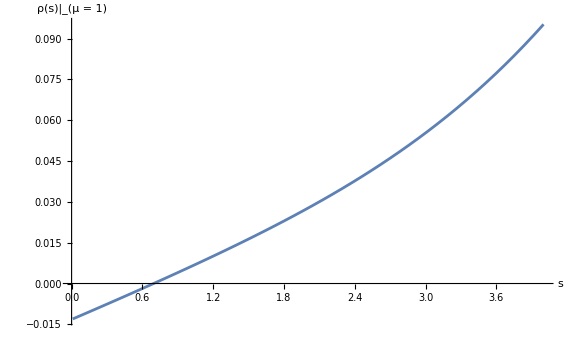
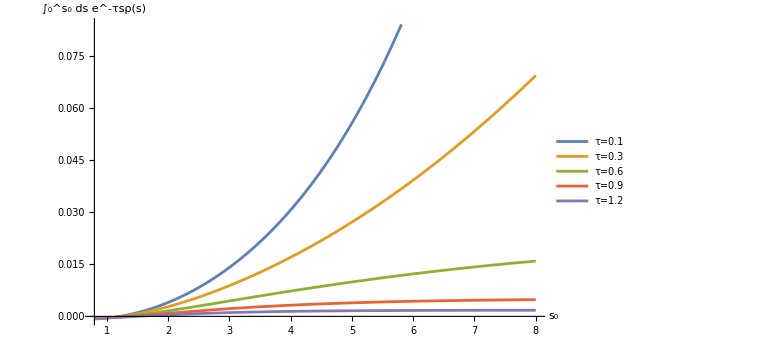

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

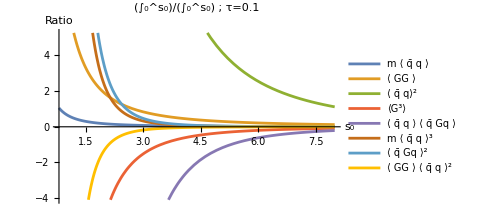
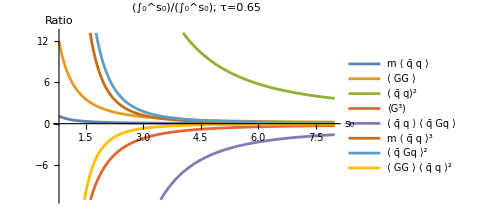
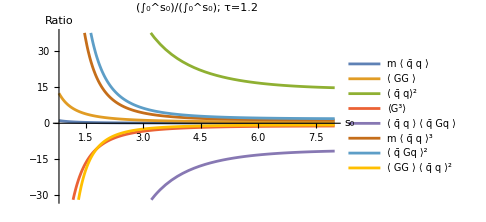

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

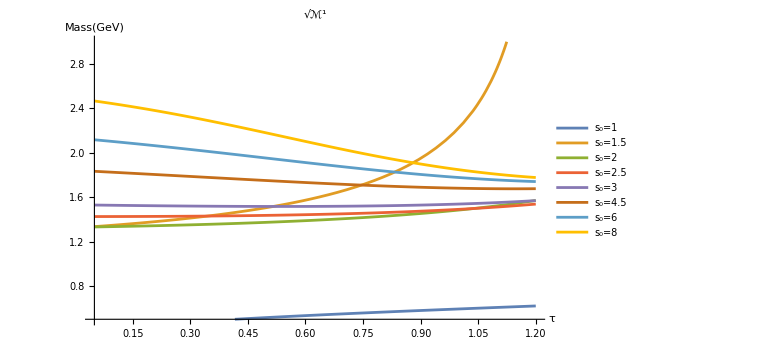
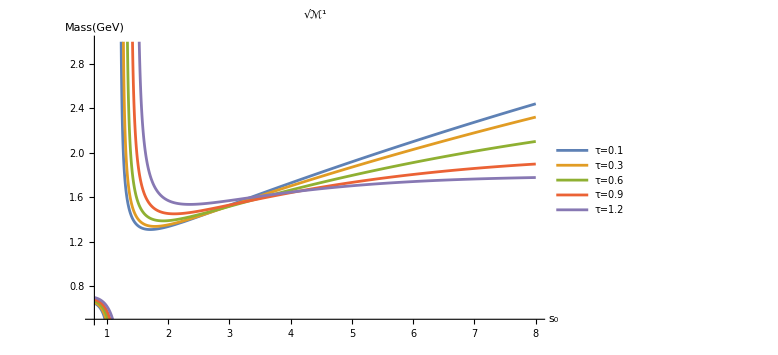

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5